## Mass Approximations

```mathematica
mWboson[k_, zL_, θH_]:=Sqrt[3/2] * k *((zL)^(-3/2)) * Sin[θH];
mZboson[mWboson_, sin2θW_]:=mWboson / Sqrt[1-sin2θW];
muTypeQuark[c0_, k_, zL_,θH_ ]:=If[c0< 0.5,
 (k/zL )*Sqrt[1 - 4 (c0)^2]Sin[θH/2],
 k *((zL)^-1/2 - c0)*Sqrt[4(c0)^2 - 1]Sin[θH/2]
];
mdTypeQuark[c0_, c1_, μ11_, μ1_, k_, zL_, θH_]:=If[c0<0.5,
k * ((zL)^(c0-c1-1)) * μ11/μ1*Sqrt[(1-2c0)(1+2c1)]*Sin[θH/2],
k * ((zL)^(-c1-1/2)) * μ11/μ1*Sqrt[(2c0 - 1)(2c1 + 1)]*Sin[θH/2]
];
meTypeLepton[c2_, c0_, μ11Prime_, μ2Tilde_, k_, zL_, θH_]:=If[ c2<0.5,
k * ((zL)^(-1+c2-c0)) * μ11Prime/μ2Tilde Sqrt[(2c0 + 1)(1-2c2)]Sin[θH/2],
k *  ((zL)^(-1/2 - c0)) * μ11Prime/μ2Tilde Sqrt[(2c0+1)(2c2-1)]Sin[θH/2]
];
mPsiDarkType[c0Prime_, k_, zL_, θH_]:=If[c0Prime< 0.5,
 k *(zL^(-1))Sqrt[1 - 4 (c0Prime)^2]Cos[θH/2],
 k *(zL^(-1/2 - c0Prime))Sqrt[4(c0Prime)^2 - 1]Cos[θH/2]
];
mνType [mu_, M_, mB_, c0_, zL_]:=-(2(mu)^2 *M* ((zL)^(2c0 + 1)))/((2c0 + 1) *(mB^2));
```

## Fermion and Boson Basis functions S, L, SR, CR, SL, CL

```mathematica
(*Bessel basis functions Subscript[FHat, αβ],Subscript[F, αβ] *)
Fab[α_, β_, u_, v_]:=BesselJ[α, u] BesselY[β, v] - BesselY[α, u]BesselJ[β, v];
FHat[α_, β_, u_, v_]:=BesselI[α, u] * BesselK[β, v] - Exp[-ⅈ(α - β ) * Pi] * BesselK[α,u] * BesselI[β,v];
FHatcPM[q_, c_, pm1_, pm2_, zL_]:=FHat[ c + pm1*1/2, c+pm2*1/2, q*(zL^(-1)), q  ];
(*   Fermions  *)
SL[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c+1/2, c+1/2, λ z, λ zL];
SR[λ_, z_, zL_, c_]:= (+π)/2 λ Sqrt[z zL]Fab[c-1/2, c-1/2, λ z, λ zL];
CR[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c-1/2, c+1/2, λ z, λ zL];
CL[λ_, z_, zL_, c_]:=(+π)/2 λ Sqrt[z zL]Fab[c+1/2, c-1/2, λ z, λ zL];



(*   Bosons   *)
Cbasis[λ_, z_, zL_]:=π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 1/2, λ z, λ zL];
Sbasis[λ_, z_, zL_]:=-π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 3/2, λ z ,λ zL];
Cprime[λ_, z_, zL_]:=π/2(λ^2) (z^(3/2)) (zL^(1/2)) Fab[1/2, 1/2, λ z, λ zL];
Sprime[λ_, z_, zL_]:=-π/2(λ^2) (z^(3/2)) (zL^(1/2))Fab[1/2, 3/2, λ z, λ zL];
```

## Effective Potential Auxiliaries

```mathematica
IntIfct[Q_, f_, q_]:= q^3 Log[1+Q*f ];
IntConst[k_, zL_] := N[(k/zL)^4/(4π)^2];
Q0[q_, c_, zL_]:= (zL/(q^2)) * 1/(FHatcPM[q, c, 1, 1, zL]*FHatcPM[q, c, -1, -1, zL]);


Qii[q_,c0_,c1_,μ1_, μ11_, zL_]:=(zL/(q^2))*( FHatcPM[q,c0,1, 1, zL]*FHatcPM[q,c0,-1, -1, zL] + ((μ1^2) *FHatcPM[q,c0,-1, -1, zL]*FHatcPM[q,c0,-1, 1, zL]*FHatcPM[q,c1,1, 1,zL]*FHatcPM[q,c1,-1, 1, zL] )/((μ11^2) * (FHatcPM[q,c1,-1, 1, zL])^2 +( FHatcPM[q,c1,1, 1, zL])^2) )^(-1);


Qiii[q_,c0_,c2_,μ2Tilde_, μ11Prime_, zL_]:= (zL/(q^2))*(FHatcPM[q,c0,1, 1, zL] * FHatcPM[q,c0,-1, -1, zL]  + ((μ2Tilde^2)*FHatcPM[q,c0,1, 1, zL]*FHatcPM[q,c0,1, -1, zL]*FHatcPM[q,c2,-1, -1, zL]*FHatcPM[q,c2,1, -1, zL])/((μ11Prime^2) * (FHatcPM[q,c2,1, -1, zL])^2 + (FHatcPM[q,c2,-1, -1, zL])^2) )^(-1)  ;



Qiv1Aux[q_,c0_,mB_, M_ , zL_, k_]:= (zL/(q^2))*(FHatcPM[q,c0,1, 1, zL] * FHatcPM[q,c0,-1, -1, zL]  - (ⅈ* (mB^2) / (k^2))/(2(ⅈ* q* (zL)^(-1) + M/k))*FHatcPM[q,c0,-1, 1, zL]*FHatcPM[q,c0,-1, -1, zL])^(-1);
Qiv1[QAux_, θH_]:=Simplify[(QAux + Conjugate[QAux])] * (Sin[1/2 θH])^2 + Simplify[QAux * Conjugate[QAux]] * (Sin[1/2 θH])^4;



h1[q_, θH_, μ11Prime_, c2_, zL_] :=(1-μ11Prime^2)(2 * (q^2)/(zL)(1+μ11Prime^2) * FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL] + 2μ11Prime^2 + (1-μ11Prime^2)*(Sin[θH])^2 ) * (Sin[θH])^2;
h2[q_,  μ11Prime_, c2_, zL_]:=((zL^2)/(q^4))* μ11Prime^4 + 2μ11Prime^4 * (zL/(q^2))*FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL] + 
(1+μ11Prime^4)(FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL])^2 +
μ11Prime^2( (FHatcPM[q,c2,-1, 1, zL]*FHatcPM[q,c2,-1, -1, zL])^2 + (FHatcPM[q,c2,1, -1, zL]*FHatcPM[q,c2,1, 1, zL])^2 );
Qiv2[q_, θH_, μ11Prime_, c2_, zL_]:=((zL^2)/(q^4))* h1[q, θH, μ11Prime, c2, zL]/h2[q, μ11Prime, c2, zL];
```

## Effective potential V_eff(θH) and Higgs Derivative.

```mathematica
(***  Up-type quark contribution ***)
VeffiFCT[q_, c0_,k_, zL_, θH_, realsList_]:= Simplify[ -12 *IntConst[k, zL] *  IntIfct[Q0[q, c0, zL], (Sin[θH/2])^2, q], {realsList∈Reals}] ;

(***  Down-type quark contribution ***)
VeffiiFCT[k_, zL_, q_, c0_, c1_, μ1_, μ11_,θH_, realsList_] :=Simplify[  -12 * IntConst[k, zL] *IntIfct[Qii[q, c0, c1, μ1, μ11, zL],(Sin[θH/2])^2, q ], { realsList∈Reals}] ;

(***  Lepton contribution contribution ***)
VeffiiiFCT[k_, zL_, q_, c0_, c2_, μ2Tilde_, μ11Prime_, θH_,  realsList_] := Simplify[-4 * IntConst[k, zL] * IntIfct[ Qiii[q, c0, c2, μ2Tilde, μ11Prime, zL],(Sin[θH/2])^2, q ] ,  {realsList∈Reals} ];

(***   Neutrino Sector  ***)
Veffiv1FCT[k_, zL_, q_, c0_, mB_, M_, θH_,  realsList_] := Simplify[-4/2 * IntConst[k, zL] * IntIfct[ Qiv1[ Qiv1Aux[q, c0, mB, M, zL, k], θH ] , 1, q] ,  {realsList∈Reals} ];
Veffiv2FCT[k_, zL_, q_, θH_, μ11Prime_, c2_,  realsList_] :=Simplify[-4 * IntConst[k, zL] * IntIfct[ Qiv2[q, θH, μ11Prime, c2, zL], 1, q] ,
{realsList∈Reals} ];


(***   Dark Fermion Contribution  ***)
VeffvFCT[k_, zL_, q_, c0Prime_, θH_,  realsList_] :=Simplify[-32 * IntConst[k, zL] * IntIfct[ Q0[q, c0Prime, zL], (Cos[θH/2])^2, q] ,
{realsList∈Reals} ];
VeffWpmFCT[ξGauge_, k_, zL_, q_, θH_]:=Simplify[2(3-ξGauge^2) * IntConst[k, zL] * IntIfct[1/2*Q0[q, 1, zL], (Sin[θH])^2,q] ,
{realsList∈Reals}  ] ;
VeffZFCT[ξGauge_, k_, zL_, q_, sin2θW_, θH_]:= Simplify [(3-ξGauge^2) * IntConst[k, zL] * IntIfct[Q0[q, 1, zL]/(2(1-sin2θW)),(Sin[θH])^2,q],
{realsList∈Reals }];
VeffAzFCT[ξGauge_, k_ , zL_, q_, θH_]:=Simplify[3ξGauge^2 * IntConst[k, zL] *  IntIfct[ Q0[q, 1, zL],(Sin[θH])^2,q ],
{realsList∈Reals } ];
Clear[zL, k, μ11, μ1,μ11Prime, μ2Tilde, c0Prime, c0,c1, c2, θHRule, θHmin, sin2θW, ξGauge, M, mB, αEM, fH, θH];
realsList = {q, c0, c1,c2 , μ1, μ11,μ2Tilde,μ11Prime,mB, M, θH, zL, k};

VeffFermionFCT =VeffiFCT[q, c0,k, zL, θH, realsList]  +
			 VeffiiFCT[k, zL, q, c0, c1, μ1, μ11,θH, realsList]+
			 VeffiiiFCT[k, zL, q, c0, c2, μ2Tilde, μ11Prime, θH,  realsList]+
				Veffiv1FCT[k, zL, q, c0, mB, M, θH,  realsList]+
				Veffiv2FCT[k, zL, q, θH, μ11Prime, c2,  realsList] +
			VeffvFCT[k, zL, q, c0Prime, θH,  realsList];
VeffBosonFct=VeffWpmFCT[ξGauge, k, zL, q, θH] +
		       VeffZFCT[ξGauge, k, zL, q, sin2θW, θH] + 
		       VeffAzFCT[ξGauge, k , zL, q, θH];


VeffFCT = VeffFermionFCT + VeffBosonFct;
HiggsDeriv = D[VeffFCT, {θH,2}];
HiggsDeriv3 = D[VeffFCT, {θH,3}];
HiggsDeriv4 = D[VeffFCT, {θH,4}];
```

## Higgs Mass auxiliaries and μ setting

```mathematica
fHfunc[k_, zL_, sin2θW_, αEM_]:=Sqrt[ (6* sin2θW) /(4 * Pi * αEM)] * (k/Sqrt[ (1-1/zL)*(zL^3 - 1) ]);
findθHMinRule[VeffFCT_, q_, θH_] := Quiet[FindMinimum[  
Quiet[NIntegrate [VeffFCT /.{θH->θHLocal}, {q, 0, ∞}]], {θHLocal,0,1}  
][[2]]];
μ11Fct[μ1_,zL_,c0_,c1_]:=(4.18/172.44)*μ1*(1/(zL^(c0-c1)))*Sqrt[(1+2 c0)/(1+2 c1)];
μ11PrimeFct[μ2Tilde_,zL_,c0_,c2_]:=Which[
c0<0.5 && c2<0.5,
(1.776/172.44)*μ2Tilde*(1/(zL^(c2-c0)))*Sqrt[(1-2 c0)/(1-2 c2)],
c0<0.5&&c2>0.5,
(1.776/172.44) *μ2Tilde*(1/(zL^(0.5-c0)))*Sqrt[(1-2 c0)/(2 c2-1)],
c0>0.5&&c2<0.5,
(1.776/172.44) *μ2Tilde*(1/(zL^(c2-0.5)))*Sqrt[(2 c0-1)/(1-2 c2)],
c0>0.5&&c2>0.5,
(1.776/172.44) *μ2Tilde*Sqrt[(2 c0-1)/(2 c2-1)]
];
```

## The full procedure

### Loading the data / setting values.

```mathematica
SetSystemOptions["MachineRealPrintPrecision"->Round[$MachinePrecision]];
Clear[zL,k,μ11,μ1,μ11Prime,μ2Tilde,c0Prime,c0,c1,c2,θHRule,θHmin,sin2θW,ξGauge,M,mB,αEM,fH,λListTop];

timeOut=25;
timeOutSolve = 15;

(* Uncomment below in the .m file *)
(*JsonNb=$ScriptCommandLine[[2]];
jsonName="dataIn"<>JsonNb<>".json";
jsonNameOut="massesOut"<>JsonNb<>".json";*)

(*Comment out in the .m, file*)
SetDirectory[NotebookDirectory[]];
jsonName = "dataInThreadNb-0.json";
jsonNameOut="massesOutThreadNb-0.json";


dataRule=Import[jsonName];
overWrite=False;
(* Constant setting function.*)
sin2θW=0.2312;
ξGauge=0;
M=-10^7;
mB=1.145*10^12;
αEM=1/127.96;
fH = fHfunc[k, zL, sin2θW, αEM];

k="k"/.dataRule;
zL="zL"/.dataRule;
c0="c0"/.dataRule;
c1="c1"/.dataRule;
c2="c2"/.dataRule;
c0Prime="c0Prime"/.dataRule;

μ1="Mu1"/.dataRule;
μ2Tilde="Mu2Tilde"/.dataRule;

μ11="Mu11"/.dataRule;
μ11Prime="Mu11Prime"/.dataRule;


k= 89130;                             
zL =35; 
c0 =0.3325; 
c1 =0.0;
c2 =-0.7;
c0Prime =0.5224;

μ1 =11.18;
μ2Tilde =0.7091;

μ11=0.108;
μ11Prime=0.108;


(*μ11=μ11Fct[μ1,zL,c0,c1];
μ11Prime=μ11PrimeFct[μ2Tilde,zL,c0,c2];
*)

mKK5 = π k /(zL-1);
replacementRules = {z->1, c0var->c0, zLvar->zL, μ1var -> μ1, μ11var -> μ11, c1var -> c1, μ2TildeVar -> μ2Tilde, μ11PrimeVar -> μ11Prime, c2var -> c2, c0PrimeVar -> c0Prime};
```

### Doing the brunt.

#### Auxiliaries.

```mathematica
return0Masses[]:={"Higgs"->0.0,"mTop"->0.0,"mBottom"->0.0,"mTau"->0.0,"mNeutrino"->0.0,"mPsiDark"->0.0,"ThetaHiggs"->0.0,"mWpm"->0.0,"mZ0"->0.0,"mZprime"->0.0, "Triviality"-> 1};
constrList = <|"Higgs"->  <|"Max"->625.0, "Min"->1.0|>, 
			 "mTop"-> <|"Max"->870.0, "Min"->1.0|>,
			"mTau"->  <|"Max"->100.0, "Min"->0.0000001|>, 
			"mBottom"->  <|"Max"->100.0, "Min"->0.0000001|>, 
			"ThetaHiggs"->  <|"Max"->1.0, "Min"->0.0|>
|>;
evalConstr[strParticle_, particleMass_]:=If[
constrList[strParticle]["Max"]>particleMass >constrList[strParticle]["Min"],
Return[True];
,
Return[False];
];
```

```mathematica
Print["---------------------------------------------------------------------------------------------------"];
Print["Started: Finding Higgs Minimum"];
Print["---------------------------------------------------------------------------------------------------"];
θHRule = TimeConstrained [findθHMinRule[VeffFCT, q, θH][[1]] , timeOut];

(*Plot[NIntegrate[VeffFCT, {q, 0, ∞}], {θH, -0.25, 0.25}, PerformanceGoal->"Speed"]*)

If[ TrueQ[Head @ θHRule==Symbol],
Print["Timeout Reached trying to find the Higgs potential minimum. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,

Print["Finished: Finding Higgs Minimum"];
Print["---------------------------------------------------------------------------------------------------"];
θHmin = Mod[θHLocal/. θHRule, π];

If[θHmin == 0 || Not[overWrite||evalConstr["ThetaHiggs", θHmin]],
Print["Trivial θH. Aborting and Returning 0 Masses."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,

(*Higgs Mass Solution*)
Print["Started: Finding Higgs Mass"];
Print["---------------------------------------------------------------------------------------------------"];
mH = Sqrt[1/fH^2 * Quiet[NIntegrate [HiggsDeriv /.{θH ->θHLocal/. θHRule}, {q, 0, ∞}]]];

If [Not[overWrite||evalConstr["Higgs", mH]] ,
Print["Higgs mass doesn't satisfy lax constraints. Aborting"];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,
Print["Finished: Finding Higgs Mass"];
Print["---------------------------------------------------------------------------------------------------"];
SL0 = SL[λ, z, zLvar, c0var];
SR0 = SR[λ, z, zLvar, c0var];

CR0 = CR[λ, z, zLvar, c0var];
CL0 =  CL[λ, z, zLvar, c0var];

SL1 = SL[λ, z, zLvar, c1var];
CR1 = CR[λ, z, zLvar, c1var];

SR2 = SR[λ, z, zLvar, c2var];
CL2 = CL[λ, z, zLvar, c2var];

SL0prime = SL[λ, z, zLvar, c0PrimeVar];
SR0prime = SR[λ, z, zLvar, c0PrimeVar];


uQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2/.replacementRules;
bQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2+((μ1var^2) SR0* CR0 * SL1 *CR1)/(μ11var^2 (CR1)^2 - (SL1)^2)/.replacementRules;
tauLeptonSol = SL0 * SR0  + (Sin[θHmin/2])^2+ (μ2TildeVar^2 SL0 CL0 SR2 CL2) / (μ11PrimeVar^2 (CL2)^2  - (SR2)^2) /.replacementRules;
psiDarkQuarkSol = SL0prime * SR0prime + (Cos[θHmin/2])^2/.replacementRules;
WbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2)/.replacementRules;
WRSol = Cbasis[λ, z, zLvar] /.replacementRules;
γTower = Cprime[λ, z, zLvar]/.replacementRules;


(*Tau Solution*)
Print["Started: Finding Tau Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
tauGuess = meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k;
λListTauGuess = TimeConstrained[NSolve[tauLeptonSol==0 && tauGuess>=λ >= 0.0, λ ∈ Reals],timeOutSolve];
λListTauFullRange  =TimeConstrained[ NSolve[tauLeptonSol==0 && mKK5/k>=λ ≥tauGuess, λ ∈ Reals],timeOutSolve];


If[TrueQ[Head @ λListTauGuess==Symbol] ||TrueQ[Head @ λListTauFullRange==Symbol] ,
Print["Timeout reached in finding the τ solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),


mTau = k*λ/.DeleteDuplicates[Join[λListTauGuess, λListTauFullRange]][[1]];

If[Not[overWrite||evalConstr["mTau", mTau] ],
Print["τ mass doesn't obey lax constraints. Aborting."];
Export[jsonNameOut,return0Masses[]];
,
Print["Finished: Finding Tau Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
Print["Started: Finding Bottom Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
(*Bottom Solution*)
bottomGuess = mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k;
λListBottomGuess= TimeConstrained[NSolve[bQuarkSol==0 && bottomGuess>=λ >= 0.0, λ ∈ Reals],timeOutSolve];
λListBottomFullRange  = TimeConstrained[NSolve[bQuarkSol==0 && mKK5/k>=λ ≥bottomGuess, λ ∈ Reals],timeOutSolve];



If[TrueQ[Head @ λListBottomGuess==Symbol] ||TrueQ[Head @ λListBottomFullRange==Symbol] ,
Print["Timeout reached in finding the Bottom Quark solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),


mBottom = λ * k /.DeleteDuplicates[Join[λListBottomGuess, λListBottomFullRange]][[1]];

If[Not[overWrite||evalConstr["mBottom", mBottom] ],
Print["Bottom quark mass doesn't obey lax constraints. Aborting."];
Export[jsonNameOut,return0Masses[]];
,
Print["Finished: Finding Bottom Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
Print["Started: Finding Top Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
(*Top Solution*)
λListTop = TimeConstrained[NSolve[uQuarkSol==0 &&  2*mKK5/k>=λ > 0, λ ∈ Reals],timeOutSolve];

If[TrueQ[Head @ λListTop==Symbol] ,
Print["Timeout reached in finding either the TopQuark solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),


mTopKKTower = k*λ/.λListTop;
mTop =mTopKKTower[[1]];


If [Not[overWrite||evalConstr["mTop", mTop]  ],
Print["Top quark mass solution doesn't obey lax constraints. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),
Print["Finished: Finding Top Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
Print["Started: Finding ΨD, W+- Solutions"];
Print["---------------------------------------------------------------------------------------------------"];

λListPsiDark = TimeConstrained[NSolve[psiDarkQuarkSol==0 && 2*mKK5/k>=λ > 0, λ ∈ Reals],timeOutSolve];
λListW = TimeConstrained[NSolve[WbosonSol==0 &&  2*mKK5/k>=λ > 0, λ ∈ Reals],timeOutSolve];

If[TrueQ[Head @ λListPsiDark==Symbol]||TrueQ[Head @ λListW==Symbol] ,
Print["Timeout reached in finding either the Ψ Dark or the W+- solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),


Print["Finished: Finding ΨD, W+- Solutions"];
Print["---------------------------------------------------------------------------------------------------"];
mWKKTower = k*λ/.λListW;
(*mTop2 = mTopKKTower[[2]];*)
mPsiDark = k*λ/.λListPsiDark[[1]];
mW = mWKKTower[[1]];
mZ   =  mW/ Sqrt[1-sin2θW];
mZprime = mWKKTower[[2]]/Sqrt[1-sin2θW];
(*****  The 10^9 is here to give the neutrino in eV *)
mTauNeutrino = mνType[mTop, M, mB, c0, zL] * 10^9;

Print["---------------------------------------------------------------------------------------------------"];
		     Print["Higgs mass of :           ",Abs[mH]," (GeV)"];
		     Print["Higgs minimum <θH> is located at :     ",Abs[θHmin]," (rads)"];
Print["---------------------------------------------------------------------------------------------------"];
Print["The 1st KK mode for the top quark: ",mTop," (GeV)"];(*Print["The 2nd KK mode for the top quark: ",mTop2];*)Print["The 1st KK mode for the bottom quark: ",mBottom," (GeV)"];Print["The 1st KK mode for the tau lepton: ",mTau," (GeV)"];Print["The 1st KK mode for the dark fermion multiplet: ",mPsiDark," (GeV)"];Print["The 1st KK mode for the W⁺⁻  bosons: ",mW," (GeV)"];Print["The 1st KK mode for the Z⁰ bosons: ",mZ," (GeV)"];Print["The 2nd KK mode for the Z⁰ bosons: ",mZprime," (GeV)"];Print["The 1st KK mode for ν_τ neutrinos: ",mTauNeutrino," (GeV)"];Print["---------------------------------------------------------------------------------------------------"];(******************Export To JSON*********************************)Export[jsonNameOut,{"Higgs"->Abs[mH],"mTop"->mTop,"mBottom"->mBottom,"mTau"->mTau,"mNeutrino"->mTauNeutrino,"mPsiDark"->mPsiDark,"ThetaHiggs"->Abs[θHmin],"mWpm"->mW,"mZ0"->mZ,(*"Mu11"->μ11,"Mu11Prime"->μ11Prime,*)"mZprime"->mZprime,  "Triviality"-> 0}];

]
]
]
]
]
]
]
]
]
]
```

---------------------------------------------------------------------------------------------------

Started: Finding Higgs Minimum

---------------------------------------------------------------------------------------------------

Finished: Finding Higgs Minimum

---------------------------------------------------------------------------------------------------

Started: Finding Higgs Mass

---------------------------------------------------------------------------------------------------

Finished: Finding Higgs Mass

---------------------------------------------------------------------------------------------------

Started: Finding Tau Solutions

---------------------------------------------------------------------------------------------------

Finished: Finding Tau Solutions

---------------------------------------------------------------------------------------------------

Started: Finding Bottom Solutions

---------------------------------------------------------------------------------------------------

Finished: Finding Bottom Solutions

---------------------------------------------------------------------------------------------------

Started: Finding Top Solutions

---------------------------------------------------------------------------------------------------

Finished: Finding Top Solutions

---------------------------------------------------------------------------------------------------

Started: Finding ΨD, W+- Solutions

---------------------------------------------------------------------------------------------------

Finished: Finding ΨD, W+- Solutions

---------------------------------------------------------------------------------------------------

---------------------------------------------------------------------------------------------------

Higgs mass of :           124.752 (GeV)

Higgs minimum <θH> is located at :     0.149481 (rads)

---------------------------------------------------------------------------------------------------

The 1st KK mode for the top quark: 170.564 (GeV)

The 1st KK mode for the bottom quark: 4.21496 (GeV)

The 1st KK mode for the tau lepton: 1.4037 (GeV)

The 1st KK mode for the dark fermion multiplet: 2043.76 (GeV)

The 1st KK mode for the W⁺⁻  bosons: 79.6698 (GeV)

The 1st KK mode for the Z⁰ bosons: 90.8629 (GeV)

The 2nd KK mode for the Z⁰ bosons: 9389.5 (GeV)

The 1st KK mode for ν_τ neutrinos: 0.0992327 (GeV)

---------------------------------------------------------------------------------------------------

### Checking section.

Higgs mass of :           124.752 (GeV)

Higgs minimum <θH> is located at :     0.149481 (rads)

---------------------------------------------------------------------------------------------------

The 1st KK mode for the top quark: 170.564

The 2nd KK mode for the top quark: mTop2

The 1st KK mode for the bottom quark: 4.21496

The 1st KK mode for the tau lepton: 1.4037

The 1st KK mode for the dark fermion multiplet: 2043.76

The 1st KK mode for the W^(+-) bosons: 79.6698

The 1st KK mode for the Z^0 bosons: 90.8629

The 2nd KK mode for the Z^0 bosons: 9389.5

The 1st KK mode for ν_τ neutrinos: 0.0992327

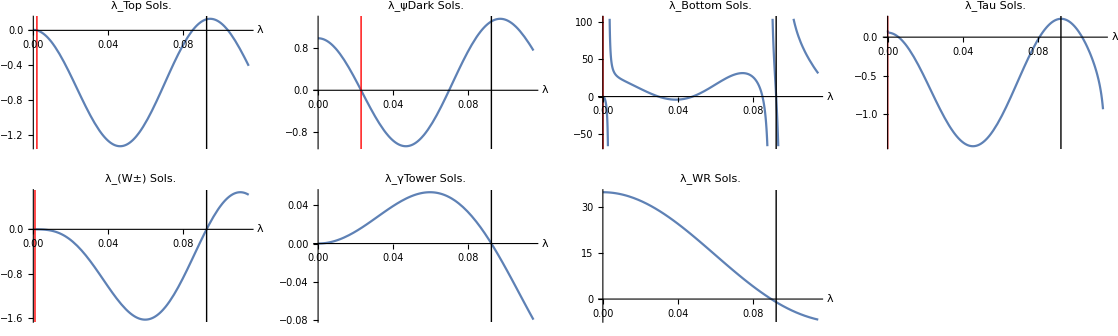

```mathematica
Print["Higgs mass of :           ",Abs[mH]," (GeV)"];
Print["Higgs minimum <θH> is located at :     ",Abs[θHmin]," (rads)"];
Print["---------------------------------------------------------------------------------------------------"]
Print["The 1st KK mode for the top quark: ", mTop];
Print["The 2nd KK mode for the top quark: ", mTop2];
Print["The 1st KK mode for the bottom quark: ", mBottom];
Print["The 1st KK mode for the tau lepton: ", mTau];
Print["The 1st KK mode for the dark fermion multiplet: ", mPsiDark];
Print["The 1st KK mode for the W^(+-) bosons: ", mW];
Print["The 1st KK mode for the Z^0 bosons: ", mZ];
Print["The 2nd KK mode for the Z^0 bosons: ", mZprime];
Print["The 1st KK mode for ν_τ neutrinos: ", mTauNeutrino];

mKK5Line = InfiniteLine[{mKK5/k,0},{0,1}];
uSolLine = InfiniteLine[{mTop/k,0},{0,1}];
psiDarkSolLine =InfiniteLine[{mPsiDark/k,0},{0,1}];
bottomQuarkSolLine =InfiniteLine[{mBottom/k,0},{0,1}];
tauSolLine=InfiniteLine[{mTau/k,0},{0,1}];
wSolLine = InfiniteLine[{mW/k,0},{0,1}];

GraphicsGrid[{
{Plot[{uQuarkSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,uSolLine}}, PlotLabel->"λ_Top Sols.", AxesLabel->Automatic] ,
Plot[{psiDarkQuarkSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,psiDarkSolLine}}, PlotLabel->"λ_ψDark Sols.", AxesLabel->Automatic],
Plot[{bQuarkSol }, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}, {Thick,Red ,bottomQuarkSolLine}}, PlotLabel->"λ_Bottom Sols.",AxesLabel->Automatic], Plot[{ tauLeptonSol}, {λ, 0, mKK5/k + π/(4zL)}  , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}, {Thick,Red ,tauSolLine}}, PlotLabel->"λ_Tau Sols.", AxesLabel->Automatic]},

{Plot[{WbosonSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,wSolLine}}, PlotLabel->"λ_(W±) Sols.", AxesLabel->Automatic],
Plot[{ γTower}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_γTower Sols.", AxesLabel->Automatic],
Plot[{ WRSol},{λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_WR Sols.", AxesLabel->Automatic]}
}]
```

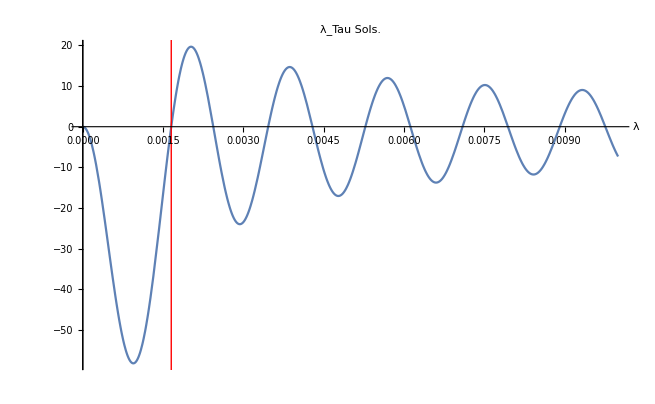

```mathematica
tauGuess = meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k;
λListTauGuess = TimeConstrained[NSolve[tauLeptonSol==0 && tauGuess>=λ >= 0.0, λ ∈ Reals],timeOutSolve];
λListTauFullRange  = TimeConstrained[NSolve[tauLeptonSol==0 && mKK5/k>=λ ≥tauGuess, λ ∈ Reals],timeOutSolve];

mTau = k*λ/.DeleteDuplicates[Join[λListTauGuess, λListTauFullRange]][[1]];


tauGuessLine = InfiniteLine[{tauGuess,0},{0,1}];
Plot[{ tauLeptonSol}, {λ, 0, 0.01}  , PlotLegends->"Expressions" ,Epilog->{{tauGuessLine}, {Thick,Red ,tauSolLine}}, PlotLabel->"λ_Tau Sols.", AxesLabel->Automatic]
```

3322.87

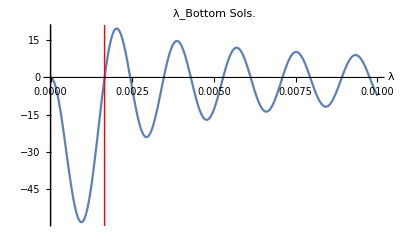

```mathematica
bottomGuess = mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k;
λListBottomGuess= NSolve[bQuarkSol==0 && bottomGuess>=λ >= 0.0, λ ∈ Reals];
λListBottomFullRange  = NSolve[bQuarkSol==0 && mKK5/k>=λ ≥bottomGuess, λ ∈ Reals];

mBottom = λ * k /.DeleteDuplicates[Join[λListBottomGuess, λListBottomFullRange]][[1]]

bottomGuessLine = InfiniteLine[{tauGuess,0},{0,1}];
Plot[{ tauLeptonSol}, {λ, 0, 0.01}  , PlotLegends->"Expressions" ,Epilog->{{bottomGuessLine}, {Thick,Red ,tauSolLine}}, PlotLabel->"λ_Bottom Sols.", AxesLabel->Automatic]
```

```mathematica
timeOutSolve = 10;
If[ TrueQ[Head @ θHRule==Symbol],
Print["Timeout Reached trying to find the Higgs potential minimum. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,


θHmin = Mod[θHLocal/. θHRule, π];


If[θHmin == 0,
Print["Trivial θH. Aborting and Returning 0 Masses."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,


(*Higgs Mass Solution*)
mH = Sqrt[1/fH^2 * Quiet[NIntegrate [HiggsDeriv /.{θH ->θHLocal/. θHRule}, {q, 0, ∞}]]];
If [Not[overWrite||evalConstr["Higgs", mH]] ,
Print["Higgs mass doesn't satisfy lax constraints."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)

,

(*Tau Solution*)
tauGuess = meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k;
λListTauGuess = TimeConstrained[NSolve[tauLeptonSol==0 && tauGuess>=λ >= 0.0, λ ∈ Reals],timeOutSolve];
λListTauFullRange  =TimeConstrained[ NSolve[tauLeptonSol==0 && mKK5/k>=λ ≥tauGuess, λ ∈ Reals],timeOutSolve];


If[TrueQ[Head @ λListTauGuess==Symbol] ||TrueQ[Head @ λListTauFullRange==Symbol] ,
Print["Timeout reached in finding the τ solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),

mTau = k*λ/.DeleteDuplicates[Join[λListTauGuess, λListTauFullRange]][[1]];

If[Not[overWrite||evalConstr["mTau", mTau] ],
Print["τ mass doesn't obey lax constraints. Aborting."];
Export[jsonNameOut,return0Masses[]];
,


(*Bottom Solution*)
bottomGuess = mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k;
λListBottomGuess= TimeConstrained[NSolve[bQuarkSol==0 && bottomGuess>=λ >= 0.0, λ ∈ Reals],timeOutSolve];
λListBottomFullRange  = TimeConstrained[NSolve[bQuarkSol==0 && mKK5/k>=λ ≥bottomGuess, λ ∈ Reals],timeOutSolve];



If[TrueQ[Head @ λListBottomGuess==Symbol] ||TrueQ[Head @ λListBottomFullRange==Symbol] ,
Print["Timeout reached in finding the Bottom Quark solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),


mBottom = λ * k /.DeleteDuplicates[Join[λListBottomGuess, λListBottomFullRange]][[1]];

If[Not[overWrite||evalConstr["mBottom", mBottom] ],
Print["Bottom quark mass doesn't obey lax constraints. Aborting."];
Export[jsonNameOut,return0Masses[]];
,

(*Top Solution*)
λListTop = TimeConstrained[NSolve[uQuarkSol==0 &&  2*mKK5/k>=λ > 0, λ ∈ Reals],timeOutSolve];

If[TrueQ[Head @ λListTop==Symbol] ,
Print["Timeout reached in finding either the TopQuark solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),


mTopKKTower = k*λ/.λListTop;
mTop =mTopKKTower[[1]];


If [Not[overWrite||evalConstr["mTop", mTop]  ],
Print["Top quark mass solution doesn't obey lax constraints. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),



λListPsiDark = TimeConstrained[NSolve[psiDarkQuarkSol==0 && 2*mKK5/k>=λ > 0, λ ∈ Reals],timeOutSolve];
λListW = TimeConstrained[NSolve[WbosonSol==0 &&  2*mKK5/k>=λ > 0, λ ∈ Reals],timeOutSolve];

If[TrueQ[Head @ λListPsiDark==Symbol]||TrueQ[Head @ λListW==Symbol] ,
Print["Timeout reached in finding either the Ψ Dark or the W+- solution. Aborting."];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*),

mWKKTower = k*λ/.λListW;
(*mTop2 = mTopKKTower[[2]];*)
mPsiDark = k*λ/.λListPsiDark[[1]];
mW = mWKKTower[[1]];
mZ   =  mW/ Sqrt[1-sin2θW];
mZprime = mWKKTower[[2]]/Sqrt[1-sin2θW];
(*****  The 10^9 is here to give us the neutrino in eV *)
mTauNeutrino = mνType[mTop, M, mB, c0, zL] * 10^9;

Print["---------------------------------------------------------------------------------------------------"];
		     Print["Higgs mass of :           ",Abs[mH]," (GeV)"];
		     Print["Higgs minimum <θH> is located at :     ",Abs[θHmin]," (rads)"];
Print["---------------------------------------------------------------------------------------------------"];
Print["The 1st KK mode for the top quark: ",mTop," (GeV)"];(*Print["The 2nd KK mode for the top quark: ",mTop2];*)Print["The 1st KK mode for the bottom quark: ",mBottom," (GeV)"];Print["The 1st KK mode for the tau lepton: ",mTau," (GeV)"];Print["The 1st KK mode for the dark fermion multiplet: ",mPsiDark," (GeV)"];Print["The 1st KK mode for the W⁺⁻  bosons: ",mW," (GeV)"];Print["The 1st KK mode for the Z⁰ bosons: ",mZ," (GeV)"];Print["The 2nd KK mode for the Z⁰ bosons: ",mZprime," (GeV)"];Print["The 1st KK mode for ν_τ neutrinos: ",mTauNeutrino," (GeV)"];Print["---------------------------------------------------------------------------------------------------"];(******************Export To JSON*********************************)Export[jsonNameOut,{"Higgs"->Abs[mH],"mTop"->mTop,"mBottom"->mBottom,"mTau"->mTau,"mNeutrino"->mTauNeutrino,"mPsiDark"->mPsiDark,"ThetaHiggs"->Abs[θHmin],"mWpm"->mW,"mZ0"->mZ,(*"Mu11"->μ11,"Mu11Prime"->μ11Prime,*)"mZprime"->mZprime}];







]
]
]
]
]
]
]
]
]
]
```

---------------------------------------------------------------------------------------------------

Higgs mass of :           124.752 (GeV)

Higgs minimum <θH> is located at :     0.149481 (rads)

---------------------------------------------------------------------------------------------------

The 1st KK mode for the top quark: 170.564 (GeV)

The 1st KK mode for the bottom quark: 4.21496 (GeV)

The 1st KK mode for the tau lepton: 1.4037 (GeV)

The 1st KK mode for the dark fermion multiplet: 2043.76 (GeV)

The 1st KK mode for the W⁺⁻  bosons: 79.6698 (GeV)

The 1st KK mode for the Z⁰ bosons: 90.8629 (GeV)

The 2nd KK mode for the Z⁰ bosons: 9389.5 (GeV)

The 1st KK mode for ν_τ neutrinos: 0.0992327 (GeV)

---------------------------------------------------------------------------------------------------